```mathematica
ClearAll[f]
Table[f[i,j,0]=RandomInteger[1],{i,-10,10},{j,-10,10}];
f[x_,y_,t_]:=f[x,y,t]=Switch[Count[{f[x+1,y,t-1],f[x-1,y,t-1],f[x,y-1,t-1],f[x,y+1,t-1]},1],2,f[x,y,t-1],3,1,_,0]
f[x_,y_,0]:=0
```

```mathematica
Manipulate[ArrayPlot[Table[f[i,j,Floor[t]],{i,-5,5},{j,-5,5}]],{t,0,10,1}]
```

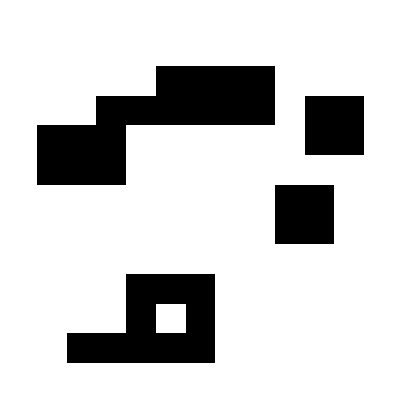

```mathematica
ArrayPlot[Table[f[i,j,100]/.{True->1,False->0},{i,-5,5},{j,-5,5}]]
```